```mathematica
(*Procesos para elegir*)
oup=OrnsteinUhlenbeckProcess[0,.1,.3];
wp=WienerProcess[2,100];
ip=ItoProcess[{ⅆx[t]==v[t]ⅆt,ⅆv[t]==-x[t]ⅆt+ⅆn[t]},x[t],{{x,v},{1,0}},t,n\[Distributed]WienerProcess[]];
```

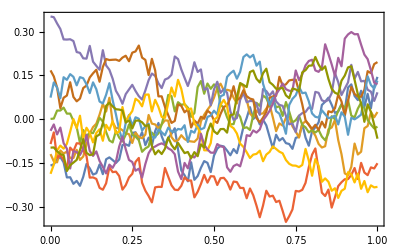

```mathematica
(*Inicialización y generación de muestra*)
n=10;
m=100;
proc=oup;
data=RandomFunction[proc,{0,10,10/m},n];
NormList[k_]:={a={};For[i=0,i≤m,i++,AppendTo[a,{i/m,data[[2]][[1]][[k]][[i+1]]}]];a}[[1]]
X=Array[NormList,n];
ListLinePlot[X,Frame->True]
```

```mathematica
(*Cálculo de profundidad vía integración y sus rangos con 4 Subscript[D, t] distintas*)
𝒟=Table[EmpiricalDistribution[Table[X[[j]][[i]][[2]],{j,n}]],{i,m+1}];
Isimp=Table[4/(m+1)∑_(k=1)^(m+1) CDF[𝒟[[k]],X[[i]][[k]][[2]]](1-CDF[𝒟[[k]],X[[i]][[k]]][[2]]),{i,n}];
Iuni=Table[1-1/(m+1)∑_(k=1)^(m+1) Abs[1/2-CDF[𝒟[[k]],X[[i]][[k]][[2]]]],{i,n}];
IL1=Table[1/(m+1)∑_(j=1)^(m+1) (1-Abs[1/n∑_(k=1)^n Sign[X[[k]][[j]][[2]]-X[[i]][[j]][[2]]]]),{i,n}];
ITukey=Table[2/(n (m+1))∑_(k=1)^(m+1) Min[Count[Table[X[[j]][[k]][[2]],{j,n}],u_/;u<X[[i]][[k]][[2]]],Count[Table[X[[j]][[k]][[2]],{j,n}],u_/;u>X[[i]][[k]][[2]]]],{i,n}];
Dsimp=Reverse[Ordering[Isimp]];
Duni=Reverse[Ordering[Iuni]];
DL1=Reverse[Ordering[IL1]];
DTukey=Reverse[Ordering[ITukey]];
```

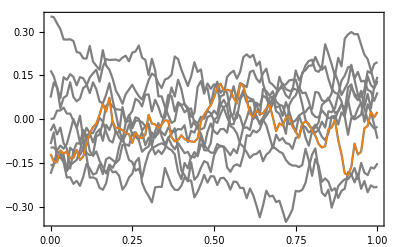

```mathematica
(*Visualización de dato más profundo*)
bgd=ListLinePlot[X,PlotStyle->Gray,Frame->True];
medI=ListLinePlot[X[[Duni[[1]]]],PlotStyle->{Thick,Orange},Frame->True];
Show[{bgd,medI}]
```

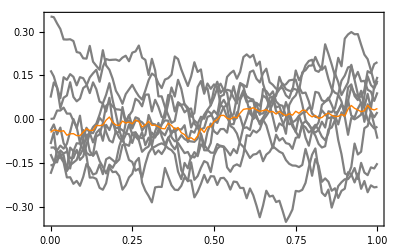

```mathematica
(*Cálculo y visualización de media truncada a nivel α*)
α=0.25;
βI=ArgMax[{β,∑_(i=1)^n Boole[ITukey[[i]]≥β]≥n-IntegerPart[α n]},β];
μI=(∑_(i=1)^n (Boole[ITukey[[i]]≥βI]X[[i]]))/(∑_(i=1)^n Boole[ITukey[[i]]≥βI]);
meanI=ListLinePlot[μI,PlotStyle->{Thick,Orange},Frame->True];
Show[{bgd,meanI}]
```

```mathematica
(*Cálculo de profundidad de bandas para ilustrar empates*)
BD=Table[∑_(j=2)^3 1/Binomial[n,j]∑_(i=1)^Binomial[n,j] ∏_(k=1)^(m+1) Boole[Min[Table[X[[Subsets[Table[a,{a,n}],{j}][[i]][[l]]]][[k]][[2]],{l,j}]]≤X[[p]][[k]][[2]]≤Max[Table[X[[Subsets[Table[a,{a,n}],{j}][[i]][[l]]]][[k]][[2]],{l,j}]]],{p,n}]
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
(*Cálculo de profundidad de bandas generalizada y sus rangos*)
GBD=1/2 Table[∑_(j=2)^3 1/Binomial[n,j]∑_(i=1)^Binomial[n,j] 1/(m+1)∑_(k=1)^(m+1) Boole[Min[Table[X[[Subsets[Table[a,{a,n}],{j}][[i]][[l]]]][[k]][[2]],{l,j}]]≤X[[p]][[k]][[2]]≤Max[Table[X[[Subsets[Table[a,{a,n}],{j}][[i]][[l]]]][[k]][[2]],{l,j}]]],{p,n}];
DGBD=Reverse[Ordering[GBD]];
```

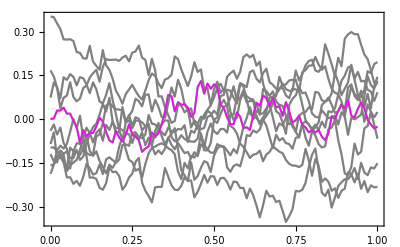

```mathematica
(*Visualización de dato más profundo*)
bgd=ListLinePlot[X,PlotStyle->Gray,Frame->True];
medGBD=ListLinePlot[X[[DGBD[[1]]]],PlotStyle->{Thick,Magenta},Frame->True];
Show[{bgd,medGBD}]
```

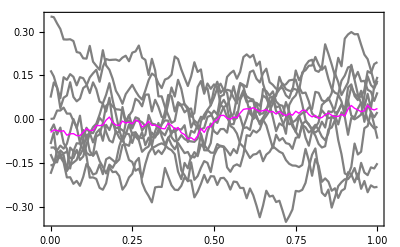

```mathematica
(*Cálculo y visualización de media truncada a nivel α*)
α=0.25;
βGBD=ArgMax[{β,∑_(i=1)^n Boole[GBD[[i]]≥β]≥n-IntegerPart[α n]},β];
μGBD=(∑_(i=1)^n (Boole[GBD[[i]]≥βGBD]X[[i]]))/(∑_(i=1)^n Boole[GBD[[i]]≥βGBD]);
meanGBD=ListLinePlot[μGBD,PlotStyle->{Thick,Magenta},Frame->True];
Show[{bgd,meanGBD}]
```

```mathematica
(*Cálculo de profundidad vía half-region (generalizada) y sus rangos*)
HRD=Table[Min[(∑_(j=1)^n ∑_(k=1)^(m+1) Boole[X[[i]][[k]][[2]]≥X[[j]][[k]][[2]]])/(m n),(∑_(j=1)^n ∑_(k=1)^(m+1) Boole[X[[i]][[k]][[2]]≤X[[j]][[k]][[2]]])/(m n)],{i,n}];
DHRD=Reverse[Ordering[HRD]];
```

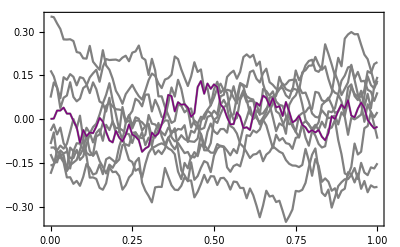

```mathematica
(*Visualización de dato más profundo*)
bgd=ListLinePlot[X,PlotStyle->Gray,Frame->True];
medHRD=ListLinePlot[X[[DHRD[[1]]]],PlotStyle->{Thick,Purple},Frame->True];
Show[{bgd,medHRD}]
```

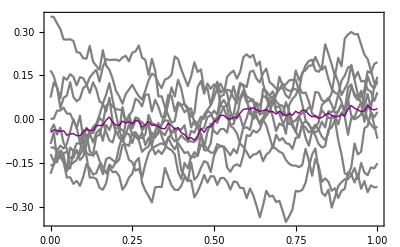

```mathematica
(*Cálculo y visualización de media truncada a nivel α*)
α=0.25;
βHRD=ArgMax[{β,∑_(i=1)^n Boole[HRD[[i]]≥β]≥n-IntegerPart[α n]},β];
μHRD=(∑_(i=1)^n (Boole[HRD[[i]]≥βHRD]X[[i]]))/(∑_(i=1)^n Boole[HRD[[i]]≥βHRD]);
meanHRD=ListLinePlot[μHRD,PlotStyle->{Thick,Purple},Frame->True];
Show[{bgd,meanHRD}]
```

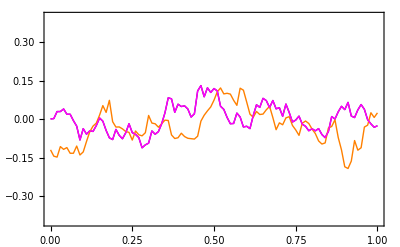

```mathematica
(*Comparación de medias truncadas*)
Show[{medHRD,medI,medGBD},PlotRange->{-0.4,0.4}]
```